```mathematica
SetDirectory["~/Code/mesons/data"];
Needs["PlotLegends`"];
```

```mathematica
bPoints=Import["bottom_points.csv"];
cPoints=Import["charm_points.csv"];

bLine=Fit[bPoints,{1,x},x]
```

9.01124+0.230043 x

```mathematica
cLine=Fit[cPoints,{1,x},x]
```

2.42771+0.296892 x

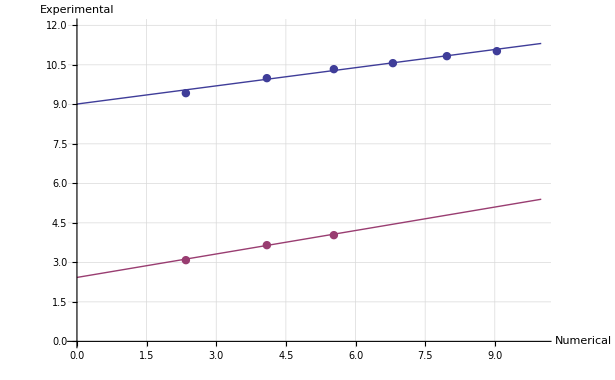

```mathematica
Show[
ListPlot[
{bPoints,cPoints},
PlotMarkers->{●,●},
PlotRange->{{0,10.01},{0,12}},
AxesLabel->{"Numerical","Experimental"},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Opacity[0.3],Dashed]
],
Plot[{bLine,cLine},{x,0,10}]
]
```